# Dataset preparation

```mathematica
ClearAll["Global`*"]
```

```mathematica
dataset=Import[FileNameJoin[{NotebookDirectory[], "dataset/dataset_full_2.wxf"}], "WXF"];
```

## Statistics

Size of dataset

```mathematica
Length@dataset
```

285830

```mathematica
keyWords=Join@@(Cases[#, x_Symbol:>ToString[HoldForm@x],Infinity,Heads->True][[2;;-1]]&/@dataset[All,"code"])//Normal;
```

```mathematica
keyWords//InputForm
```

```mathematica
Length@keyWords
```

16725286

```mathematica
Counts[keyWords]
```

<|CompoundExpression→105565,Print→813,a→21976,Abort→124,b→13076,TimeConstrained→89,Pause→188,MemoryConstrained→14,Range→4438,Power→95632,79779,IPTCRaw→5,MakerNote→5,CopyMetaInformation→1,overwriteAllTags→2,inFPath→4,outFPath→4,GetXMP→1,tname→25,GetIPTC→1,GetExif→1|>
 |  |  |  |

```mathematica
expCounts=%49;
```

```mathematica
expCountsSorted=Sort[expCounts,Greater];
```

```mathematica
expCountsSortedDS=Dataset@expCountsSorted;
```

```mathematica
Length@expCountsSorted
```

79799

```mathematica
expCountsSortedFiltered=Sort[Association[(#-> expCountsSorted[#])&/@Names["System`*"]],Greater]
```

<|List→12543469,Rule→380749,Set→180779,Times→156783,CompoundExpression→105565,Null→101174,6578,$CloudExpressionBase→3,$SecuredAuthenticationKeyTokens→Missing[KeyAbsent,$SecuredAuthenticationKeyTokens],$Services→43,$SessionID→25,$ServiceCreditsAvailable→15,$SetParentLink→1|>
 |  |  |  |

```mathematica
ListLogPlot[expCountsSortedFiltered[[1;;5]],PlotRange->All,Filling->Bottom, PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
SpokenString[dataset[[1,"code"]]//Normal]
```

HoldComplete of the quantity print a semicolon abort semicolon print b

```mathematica
dataset
```

Dataset[<>]

## Label Extracting

```mathematica
codeArray = Normal[dataset][[All, "code"]];
```

```mathematica
codeSetArray=codeArray/.{
HoldComplete[(SetDelayed|Set)[(x_[___]|x_),y___]] :>{ToString[HoldForm[x]],HoldComplete[y]},
HoldComplete[CompoundExpression[(SetDelayed|Set)[(x_[___]|x_),y___],___]] :>{ToString[HoldForm[x]],HoldComplete[y]},
HoldComplete[y___]:> {Undefined,HoldComplete[y]}
};
```

```mathematica
codeSetArrayClean=Cases[codeSetArray,{_String,HoldComplete[___]},{1,2}];
```

```mathematica
codeSetArrayClean//Length
```

130540

{{in,HoldComplete[CreateTemporary[]]},{Undefined,HoldComplete[Null]},{out,HoldComplete[CreateTemporary[]]}}

```mathematica
names=First[#]&/@codeSetArrayClean;
```

```mathematica
uniqNames=DeleteDuplicates[names];
```

```mathematica
uniqNames//Length
```

30335

```mathematica
Dataset@Sort[Counts[names],Greater]
```

Dataset[<>]

```mathematica
names = AssociationMap[True &,Names["System`*"]];
```

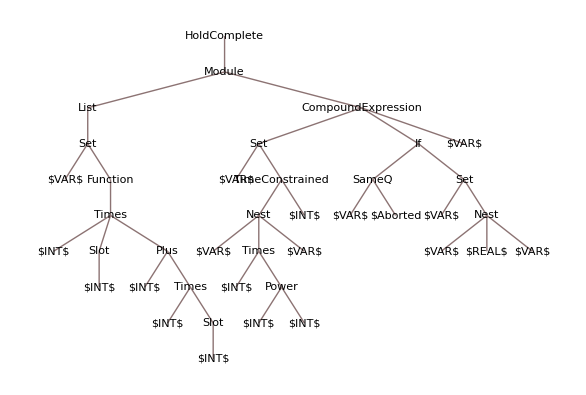

```mathematica
ReplaceAll[
codeSetArrayClean[[1]][[2]],{
s:_Integer:>RuleCondition["$INT$"],
 s:_Real:>RuleCondition["$REAL$"], 
s:_String:>RuleCondition["$STR$"],
s:_Symbol/;names[ToString[Unevaluated[s]]]:>RuleCondition[SymbolName[Unevaluated[s]]],
s:_Symbol:>RuleCondition["$VAR$"]
}
]//TreeForm
```

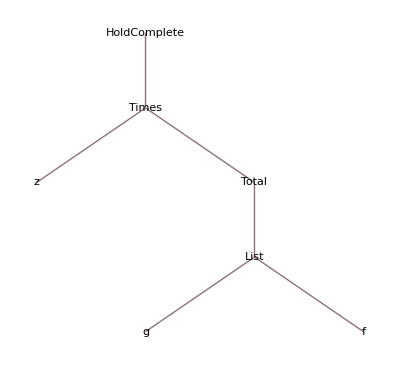

5

```mathematica
xpr=HoldComplete[z Total@{g,f}];
xpr//TreeForm
Depth@xpr
Level[xpr,{1,-2}]
```

```mathematica
MapIndexed
```

```mathematica
HoldForm@a//Depth
```

2

```mathematica
a+b//HoldComplete//FullForm
```

HoldComplete[Plus[a,b]]

```mathematica
ClearAll[getGraph];
SetAttributes[getGraph,HoldAllComplete];
getGraph[expr_,id_Integer:0]/;Depth[expr]>2:=(
idx=id+1;
(expr/.HoldComplete[h_[a___]]:>Echo[a]);
{idx,Echo[expr]/.HoldComplete[h_[a___]]:>h}
);
getGraph[expr_,id_Integer:0]:={id,expr};
```

```mathematica
getGraph[HoldComplete[a+b]]
```

b a

HoldComplete[a+b]

{1,Plus}

```mathematica
DownValues[getGraph]
```

{HoldPattern[getGraph[expr_]/;Depth[expr]≤2]:>expr,HoldPattern[getGraph[expr_]]:>expr}

```mathematica
Graph
```

## Token Sequence

### Lab

```mathematica
exp=dataset[[3]][["code"]]//Normal
```

HoldComplete[MemoryConstrained[Range[10^6],10000]]

```mathematica
{HoldComplete,MemoryConstrained,Range,Power, Intger, Integer}
```

```mathematica
heads = Cases[exp, _Symbol,Infinity,Heads->True]
```

{HoldComplete,MemoryConstrained,Range,Power}

```mathematica
Position[exp,Alternatives @@ heads]
```

{{0},{1,0},{1,1,0},{1,1,1,0}}

```mathematica
pos = Position[exp,MemoryConstrained]
```

{{1,0}}

```mathematica
Map[exp[[Sequence @@ #]]&,pos]
```

{MemoryConstrained}

```mathematica
Map[# -> Position[exp, #]&, heads]
```

{HoldComplete→{{0}},MemoryConstrained→{{1,0}},Range→{{1,1,0}},Power→{{1,1,1,0}}}

```mathematica
5
```

```mathematica
replaced = ReplaceAll[exp, s:_Integer|_Real|_String :> Block[{}, Type[Head[s], s] /; True]]
```

HoldComplete[MemoryConstrained[Range[Type[Integer,10]^Type[Integer,6]],Type[Integer,10000]]]

```mathematica
Cases[replaced, _Type, Infinity]
```

{Type[Integer],Type[Integer],Type[Integer]}

```mathematica
1.2//FullForm
```

1.2

### Extract

```mathematica
names = AssociationMap[True &,Names["System`*"]]; (*hash*)
ClearAll[getTokenSeq]
getTokenSeq[expr_]:=Rest @Flatten[
Last[
Reap[
 ReplaceAll[
expr,{
$DATA$:> RuleCondition[Sow@"$DATA$"],
s:_Integer:>RuleCondition[Sow@"$INT$"],
 s:_Real:>RuleCondition[Sow@"$REAL$"], 
s:_String:>RuleCondition[Sow@"$STR$"],
s:_Symbol/;names[ToString[Unevaluated[s]]]:>RuleCondition[Sow@SymbolName[Unevaluated[s]]],
s:_Symbol:>RuleCondition[Sow@"$VAR$"]
}
]
]
]
]
```

```mathematica
n=0;
ProgressIndicator[Dynamic[n],{1,Length[dataset]}]

tokens =  Map[
Function[n++;getTokenSeq[#]],
dataset
];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "dataset/dataset_token_sequence_2.wxf"}], tokens,"WXF"]
```

/Users/ckorikov/___wss19/WSS-19/Final Project/Research/dataset/dataset_token_sequence_2.wxf

```mathematica
Dataset@tokens
```

Dataset[<>]

## Paths Check

```mathematica
test=Import[FileNameJoin[{NotebookDirectory[], "dataset/dataset_token_sequence.wxf"}]];
```

{{CompoundExpression,Print,$VAR$,Abort,Print,$VAR$},{TimeConstrained,Pause,$INT$,$INT$},{MemoryConstrained,Range,Power,$INT$,$INT$,$INT$},285825,{End},{End}}
 |  |  |  |

```mathematica
Cases[test,{("Set"|"SetDelayed"),___}]//Length
```

70718